```mathematica
f[x_,y_,r_]:=x^2+y^2-r^2
```

```mathematica
fr[r_,al_]:={r Cos[al],r Sin[al]}
```

```mathematica
df[{x_,y_,r_}]:=√(r^2-x^2)+x/y
```

```mathematica
fr[4.,Pi]
```

{-4.,0.}

```mathematica
df[Flatten[{fr[4.,Pi*0.0001],4}]]
```

3183.1

```mathematica
ArcTan[%]
```

1.32582

```mathematica
Pi/6.
```

0.523599

```mathematica
yx[x_,r_]:=√(r^2-x^2)
```

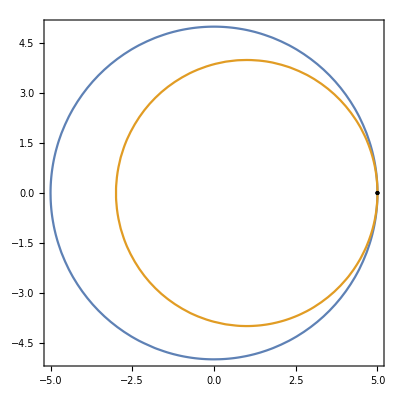

```mathematica
ContourPlot[{f[x,y,5]==0,f[x-1,y,4]==0},{x,-5,5},{y,-5,5},Epilog->Point[point/.{a->5}]]
```

```mathematica
point= {x,y}/.Solve[{f[x,y,a]==0,f[x-1,y,4]==0},{x,y}]
```

{{1/2 (-15+a^2),-1/2 √(-225+34 a^2-a^4)},{1/2 (-15+a^2),1/2 √(-225+34 a^2-a^4)}}

```mathematica
Reduce[yx[x-1,4]==yx[x,4],x]
```

x==1/2

```mathematica
yx[1/2,4]
```

(3 √7)/2

```mathematica
ClearAll[yx]
```

```mathematica
point/.{a->4}
```

{{1/2,-(3 √7)/2},{1/2,(3 √7)/2}}

```mathematica
Solve[-225+34 a^2-a^4==0,a]
```

{{a→-5},{a→-3},{a→3},{a→5}}

```mathematica
D[f[x,y,r],{x}]
```

2 x

```mathematica
D[yx[x,r],{x}]
```

-x/(√(r^2-x^2))

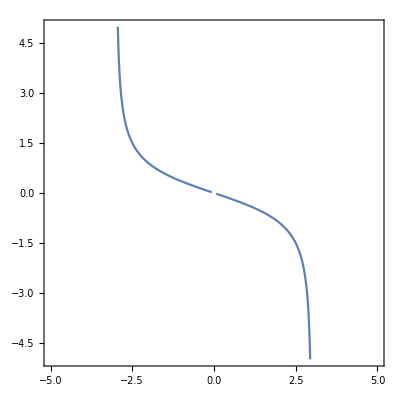

```mathematica
ContourPlot[df[x,y,3]==0,{x,-5,5},{y,-5,5},PlotPoints->100]
```